Cómo guardar cosas

Wolfram Language facilita el proceso de guardar cosas, ya sea en Wolfram Cloud, o bien localmente en la propia computadora. Se tratará primero lo relativo a Wolfram Cloud.

En Wolfram Cloud, cualquier cosa es un objeto en la nube, especificado mediante un UUID (identificador universal único).

A todo objeto en la nube se le asigna de inmediato un UUID:

```mathematica
CloudObject[ ]
```

CloudObject[]

Al momento de crear un objeto en la nube, se le asigna un UUID largo, generado aleatoriamente. Lo interesante de los UUIDs es que puede asegurarse que nunca habrá dos iguales asignados a objetos diferentes. (Hay más de 300 billones (10^12) de billones de billones concebibles como UUIDs Wolfram).

Ponga en la nube una expresión de Wolfram Language:

```mathematica
CloudPut[{-Graphics-,-Graphics-}]
```

CloudObject[]

Traiga de regreso de la nube esa expresión:

```mathematica
CloudGet[%]
```

{-Graphics-,-Graphics-}

Las definiciones que se hayan hecho usando = y := pueden guardarse usando CloudSave. (Si dichas definiciones dependen de otras definiciones, estas también se guardan). Esas definiciones se recuperan en una nueva sesión usando CloudGet.

Haga una definición:

```mathematica
colorlist[n_Integer]:=RandomColor[n]
```

Guárdela en la nube mediante CloudGet para recuperarla posteriormente:

```mathematica
CloudSave[colorlist]
```

CloudObject[]

CloudPut permite guardar expresiones individuales de Wolfram Language. ¿Y cómo acumular expresiones progresivamente, ya sea de Wolfram Language o, por ejemplo, de un dispositivo o sensor externo?

Wolfram Data Drop sirve exactamente para este propósito. Se comienza por crear un databin, lo que se hace usando CreateDatabin en Wolfram Language:

Cree un databin:

```mathematica
bin=CreateDatabin[ ]
```

Databin[…]

Se añade información a este databin desde cualquier tipo de dispositivo o servicio externos, al igual que usando la función DatabinAdd en Wolfram Language.

Añada algo a un databin:

```mathematica
DatabinAdd[bin,{1,2,3,4}]
```

Databin[…]

Añada algo más al mismo databin:

```mathematica
DatabinAdd[bin,{a,b,c}]
```

Databin[]

Traiga los valores guardados en el databin:

```mathematica
Values[bin]
```

{{1,2,3,4},{a,b,c}}

He aquí un databin que ha acumulado datos provenientes de un sensor en el escritorio del autor. DateListPlot grafica la serie cronológica de dichos datos.

Use un identificador abreviado referido a un databin conectado con sensores en el escritorio:

```mathematica
Databin["7m3ujLVf"]
```

Databin[…]

Grafique las series cronológicas del databin:

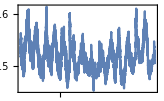
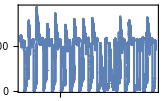
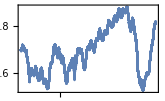
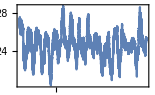
<|humidity→-Graphics-,light→-Graphics-,pressure→-Graphics-,temperature→-Graphics-|>

```mathematica
DateListPlot[Databin["7m3ujLVf"]]
```

Al igual que CloudPut y CloudSave, Wolfram Data Drop guarda información en la nube. Pero quizá se desee guardar las cosas en una computadora local, sobre todo si no se está conectado con la nube. Si ya se sabe en qué parte del sistema de archivos se desea que queden los archivos, puede usarse Put, Save y Get para guardarlos y recuperarlos posteriormente.

Wolfram Language también puede decidir automáticamente sobre una ubicación local “anónima”. Esto se hace mediante LocalObject.

Genere una ubicación “anónima” para Put, Save, etc.:

```mathematica
LocalObject[ ]
```

LocalObject[file:///Users/sw/Library/Wolfram/Objects/365e034d-9830-4842-8681-75d3714b3d19]

Coloque una imagen en esa ubicación:

```mathematica
Put[-Graphics-,%]
```

LocalObject[file:///Users/sw/Library/Wolfram/Objects/365e034d-9830-4842-8681-75d3714b3d19]

Traiga la imagen de regreso:

```mathematica
Get[%]
```

-Graphics-

Vocabulario

CloudObject[ ] |   | crea un objeto en la nube
CloudPut[expr] |   | pone en la nube
CloudGet[obj] |   | trae de la nube 
CloudSave[s] |   | guarda definiciones en la nube
Databin["id"] |   | un databin con información acumulada
CreateDatabin[ ] |   | crea un nuevo databin
DatabinAdd[obj,valor] |   | añade algo a un databin
DateListPlot[data] |   | construye un gráfico de una lista de fechas
LocalObject[ ] |   | crea un objeto local
Put[expr,obj] |   | pone en un objeto local
Get[obj] |   | trae desde un objeto local

Preguntas y respuestas

¿Qué significan las letras y números en los UUIDs?

Son dígitos en hexadecimal (base 16); las letras de la “a” a la “f” son los dígitos hex del 10 al 15. Cada UUID tiene 32 dígitos hex, que corresponden a 16^32≈3×10^38 posibilidades.

¿Cómo se compara el número de UUIDs posibles con otras cosas?

Es más o menos como el número de átomos en un kilómetro cúbico de agua, o como 100 billones (= 100×10^12) de veces el número de estrellas en el universo. Si cada una de los 50 mil millones de computadoras en la Tierra generara un UUID a 10 GHz, le tomaría la edad del universo para agotar la disponibilidad de UUIDs.

¿Cómo se relacionan los UUIDs con los IDs abreviados?

Todos los IDs abreviados, en la forma como se generan con URLShorten, se registran explícitamente, y se garantiza que son únicos, más o menos como los nombres de los dominios en internet. Los UUIDs son suficientemente largos como para asumir que son únicos, aun si no hubiera ningún tipo de registro central.

¿Se puede especificar el nombre de un archivo en CloudObject, CloudPut, etc.?

Sí. Y el nombre del archivo estará relacionado con la correspondiente carpeta de usuario en la nube. El archivo recibirá también un URL, que incluye la base de la nube que se esté usando, así como la ID del usuario.

¿Pueden personas ajenas acceder a lo que uno tiene guardado dentro de un objeto en la nube?

Por lo general, no. Claro que, si se habilita la opción Permissions→"Public", entonces cualquiera puede tener acceso, tal y como se dijo respecto de las aplicaciones en la web en la Sección 36. También uno puede especificar a quién se permite el acceso y qué es lo que tiene permiso de hacer.

¿Se puede trabajar con databins sin usar Wolfram Language?

Sí. Puede usarse la web y muchos otros sistemas para crear y añadir cosas a databins.

¿Existe alguna manera de manipular una expresión en la nube, sin traer de ahí la expresión completa?

Sí. Para ello se hace una expresión en la nube (usando CreateCloudExpression). Así, todas la formas usuales de traer y formar partes de la expresión pueden funcionar, aunque la expresión estará persistentemente guardada en la nube.

Notas técnicas

Cuando se trabaja en la nube, los documentos Wolfram Notebook se guardan automáticamente cada vez que se hace un cambio, a menos que se especifique lo contrario.

Se pueden guardar objetos grandes de manera más eficiente con DumpSave que con Save, pero el archivo así creado queda en binario, y no en texto.

LocalCache[CloudObject[...]] es una forma de referirse a un objeto en la nube, pero usando una caché local de su contenido si está disponible (y crearla, si no lo está).

Los archivos de datos pueden tener signaturas de datos, que especifican cómo deben interpretarse los datos que contienen, por ejemplo, en términos de unidades, formatos de fechas, etc.

Una asignación como x=3 se mantiene solamente mientras dura una sesión con Wolfram Language. Pero se pueden usar cosas como PersistentValue["x"]=3 para guardar valores con diferentes grados de persistencia (en una sola computadora; cada vez que se inicia una sesión; por un tiempo determinado; etc.).

Para explorar más

Guía para archivos en Wolfram Language »

Wolfram Data Drop »